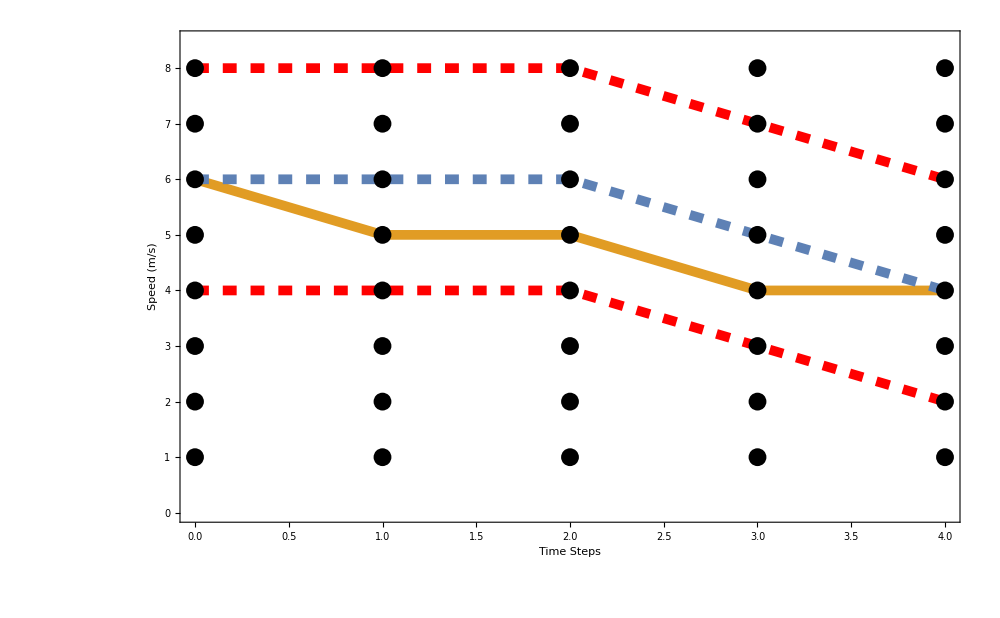

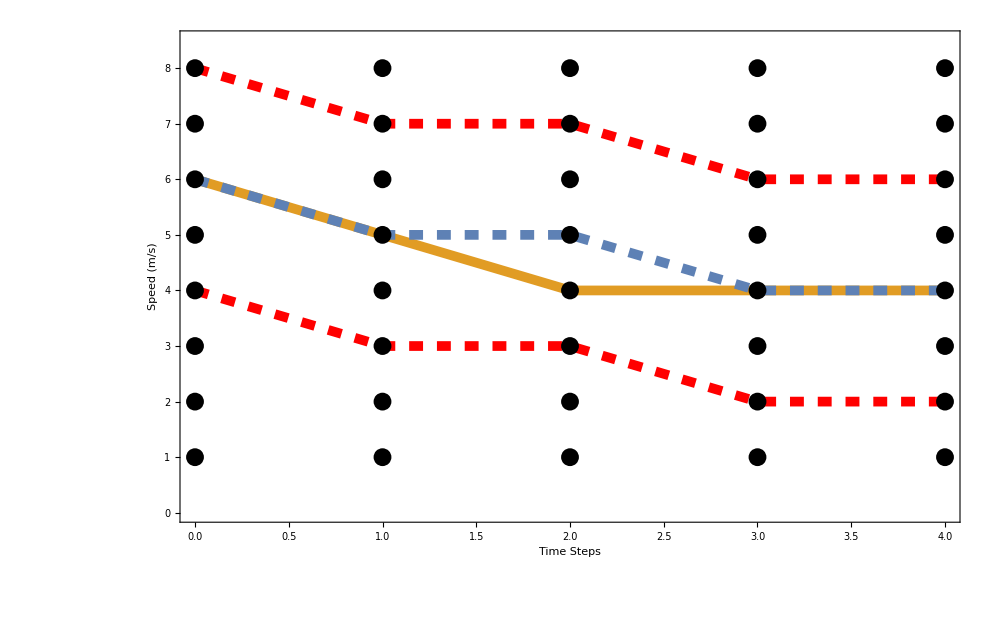

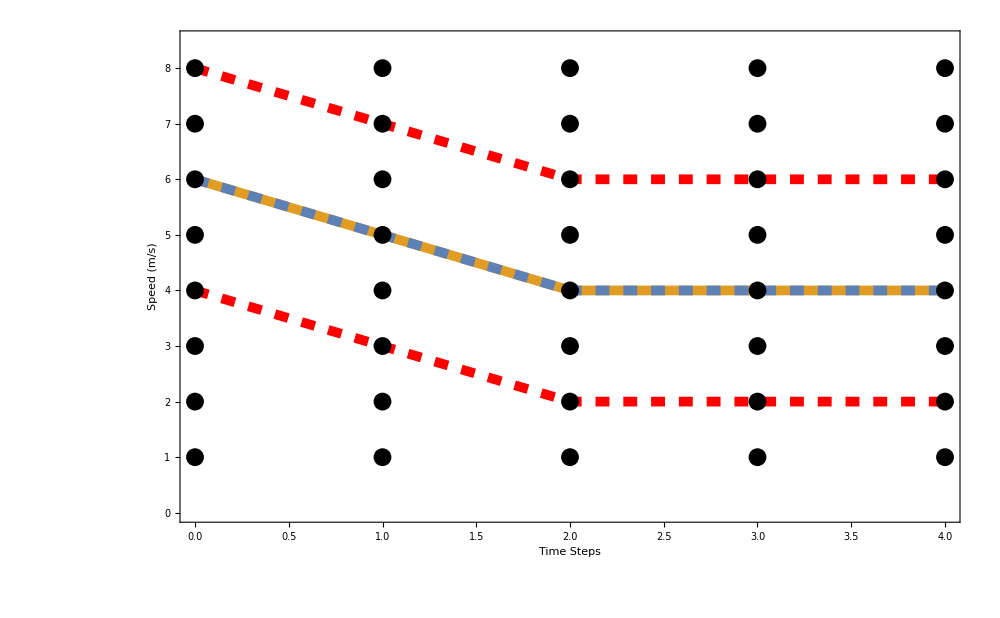

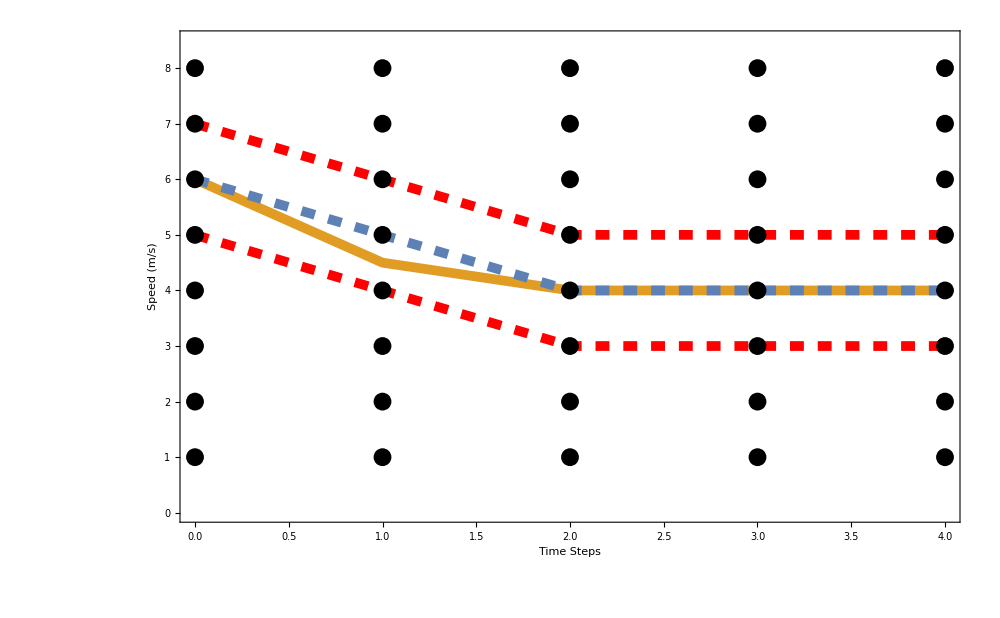

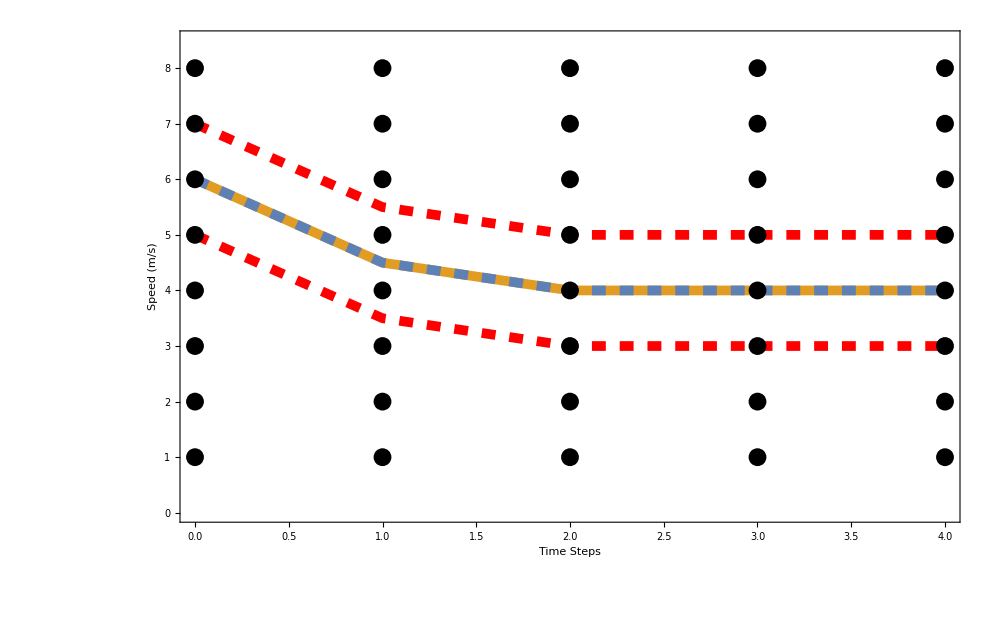

```mathematica
ClearAll["Global'*"]

dataFolder=StringJoin[NotebookDirectory[],"outputs"];
SetDirectory[dataFolder];
files=FileNames[];

pos={};speed={};accel={};vmin={};vmax={};xmin={};xmax={};initx={};initv={};inita={};
(*For[i=1,i≤Length[files]-1,i++,
data=Import[files[[i]],"Table"];
steps=data[[2;;,1]];
controlSteps=Delete[data[[2;;,1]],Length[steps]];
AppendTo[pos,data[[2;;,2]]];
AppendTo[speed,data[[2;;,3]]];
AppendTo[accel,Drop[data[[2;;,4]],-1]];
AppendTo[vmin,data[[2;;,13]]];
AppendTo[vmax,data[[2;;,14]]];
AppendTo[xmin,data[[2;;,15]]];
AppendTo[xmax,data[[2;;,16]]];
AppendTo[initv,data[[2;;,17]]];
AppendTo[initx,data[[2;;,18]]];
AppendTo[inita,Drop[data[[2;;,19]],-1]];
]*)
steps={0,1,2,3,4};

initv={{6,6,6,5,4},
	{6,5,5,4,4},
	{6,5,4,4,4},
	{6,5,4,4,4},
	{6,4.5,4,4,4}};
speed={{6,5,5,4,4},
	{6,5,4,4,4},
	{6,5,4,4,4},
	{6,4.5,4,4,4},
	{6,4.5,4,4,4}};
vmax={{8,8,8,7,6},
	{8,7,7,6,6},
	{8,7,6,6,6},
	{7,6,5,5,5},
	{7,5.5,5,5,5}};
vmin={{4,4,4,3,2},
	{4,3,3,2,2},
	{4,3,2,2,2},
	{5,4,3,3,3},
	{5,3.5,3,3,3}};

defBlue=ColorData[97,1];
defOrange=ColorData[97,2];
defGreen=ColorData[97,3];
fontSize=58;
(*n = Length[files];*)
n = 6;
SetDirectory[NotebookDirectory[]];

(*lp=ListLinePlot[{Legended[Transpose[{steps,speed[[1]]}],Placed["Optimal",Above]],Legended[Transpose[{steps,initv[[1]]}],Placed["Received",Above]],Legended[Transpose[{steps,vmax[[1]]}],Placed["Corridor",Above]],Transpose[{steps,vmin[[1]]}]},
Filling->None,Joined->True,GridLines->None,PlotRange->{Automatic,{0,8.5}},LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Dashing[0.01],Red},{Thickness[0.007],Dashing[0.01],Red}},
AxesStyle->Thickness[0.001],ImageSize->1000,PlotStyle->PointSize[Large],Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{"Time Steps","Speed (m/s)",None,None}];*)

lp=ListLinePlot[{Transpose[{steps,speed[[1]]}],Transpose[{steps,initv[[1]]}],Transpose[{steps,vmax[[1]]}],Transpose[{steps,vmin[[1]]}]},
Filling->None,Joined->True,GridLines->None,PlotRange->{Automatic,{0,8.5}},LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Dashing[0.01],Red},{Thickness[0.007],Dashing[0.01],Red}},
AxesStyle->Thickness[0.001],ImageSize->1000,PlotStyle->PointSize[Large],Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{"Time Steps","Speed (m/s)",None,None}];
lp2=ListLinePlot[{Transpose[{steps,speed[[2]]}],Transpose[{steps,initv[[2]]}],Transpose[{steps,vmax[[2]]}],Transpose[{steps,vmin[[2]]}]},
Filling->None,Joined->True,GridLines->None,PlotRange->{Automatic,{0,8.5}},LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Dashing[0.01],Red},{Thickness[0.007],Dashing[0.01],Red}},
AxesStyle->Thickness[0.001],ImageSize->1000,PlotStyle->PointSize[Large],Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{"Time Steps","Speed (m/s)",None,None}];
lp3=ListLinePlot[{Transpose[{steps,speed[[3]]}],Transpose[{steps,initv[[3]]}],Transpose[{steps,vmax[[3]]}],Transpose[{steps,vmin[[3]]}]},
Filling->None,Joined->True,GridLines->None,PlotRange->{Automatic,{0,8.5}},LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Dashing[0.01],Red},{Thickness[0.007],Dashing[0.01],Red}},
AxesStyle->Thickness[0.001],ImageSize->1000,PlotStyle->PointSize[Large],Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{"Time Steps","Speed (m/s)",None,None}];
lp4=ListLinePlot[{Transpose[{steps,speed[[4]]}],Transpose[{steps,initv[[4]]}],Transpose[{steps,vmax[[4]]}],Transpose[{steps,vmin[[4]]}]},
Filling->None,Joined->True,GridLines->None,PlotRange->{Automatic,{0,8.5}},LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Dashing[0.01],Red},{Thickness[0.007],Dashing[0.01],Red}},
AxesStyle->Thickness[0.001],ImageSize->1000,PlotStyle->PointSize[Large],Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{"Time Steps","Speed (m/s)",None,None}];
lp5=ListLinePlot[{Transpose[{steps,speed[[5]]}],Transpose[{steps,initv[[5]]}],Transpose[{steps,vmax[[5]]}],Transpose[{steps,vmin[[5]]}]},
Filling->None,Joined->True,GridLines->None,PlotRange->{Automatic,{0,8.5}},LabelStyle->{FontFamily->"Constantia", FontSize->fontSize,Bold},
PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue},{Thickness[0.007],Dashing[0.01],Red},{Thickness[0.007],Dashing[0.01],Red}},
AxesStyle->Thickness[0.001],ImageSize->1000,PlotStyle->PointSize[Large],Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{"Time Steps","Speed (m/s)",None,None}];


(*points={   {0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8}};*)
points={   {0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8}};
p=ListPlot[points,PlotStyle->{Black}];
s1=Show[lp,p]
s2=Show[lp2,p]
s3=Show[lp3,p]
s4=Show[lp4,p]
s5=Show[lp5,p]

Export["example1.png",s1,ImageResolution->100];
Export["example2.png",s2,ImageResolution->100];
Export["example3.png",s3,ImageResolution->100];
Export["example4.png",s4,ImageResolution->100];
Export["example5.png",s5,ImageResolution->100];
```